```mathematica
λ=143.095I+3.62275;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→-5.28792+3.54706 ⅈ},{z→-0.0509939-7.07507 ⅈ},{z→5.34104+3.44419 ⅈ}}

-5.28792+3.54706 ⅈ

-0.0509939-7.07507 ⅈ

5.34104+3.44419 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

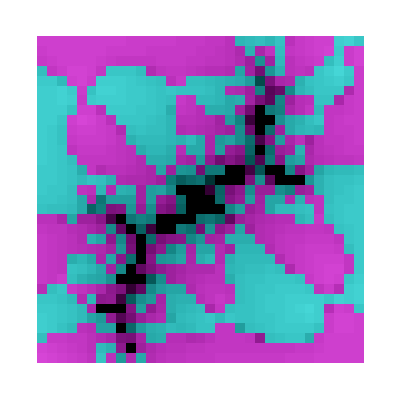

```mathematica
numberPoints =32;
limIterations=50;
xxMin=Re[z2]-1; xxMax=Re[z2]+1; yyMin=Im[z2]-1; yyMax=Im[z2]+1;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
numberPoints =512;
limIterations=50;
xxMin=-200; xxMax=200; yyMin=75; yyMax=300;
plotColorFractal[iterSch, numberPoints]
```

-Graphics-

```mathematica
numberPoints =512;
limIterations=50;
xxMin=-0.5; xxMax=5; yyMin=-33/4; yyMax=-1;
plotColorFractal[iterSch, numberPoints]
```

-Graphics-

```mathematica
numberPoints =512;
limIterations=50;
xxMin=1.5; xxMax=2.5; yyMin=-37/8; yyMax=-45/16;
plotColorFractal[iterSch, numberPoints]
```

-Graphics-

```mathematica
NestList[sp,z1,100]
```

{-5.28792+3.54706 ⅈ,-0.394224-0.226365 ⅈ,-0.76178-0.289345 ⅈ,-1.04254-0.079749 ⅈ,-1.00187+0.0034475 ⅈ,-1.-6.38582×10^-6 ⅈ,-1.+2.73748×10^-11 ⅈ,-1.-2.95216×10^-22 ⅈ,-1.+4.70198×10^-38 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ}

```mathematica
NestList[sp,z2,20000]
```

{-0.0509939-7.07507 ⅈ,-0.003834+0.456434 ⅈ,-0.0145552+1.14658 ⅈ,-0.670539-7.15829 ⅈ,-0.00262555+0.453202 ⅈ,-0.00981935+1.13428 ⅈ,-0.541477-7.80793 ⅈ,0.00192215+0.459296 ⅈ,0.00760762+1.15768 ⅈ,0.303012-6.73121 ⅈ,-0.00156912+0.456323 ⅈ,-0.00585913+1.14623 ⅈ,-0.274472-7.23011 ⅈ,-0.00321462+0.456235 ⅈ,-0.0121703+1.14584 ⅈ,-0.56823-7.21181 ⅈ,-0.00242205+0.454352 ⅈ,-0.00907747+1.13866 ⅈ,-0.470241-7.58216 ⅈ,-0.000288796+0.457355 ⅈ,-0.000948875+1.1502 ⅈ,-0.043615-7.06019 ⅈ,-0.00383206+0.456436 ⅈ,-0.0145478+1.14659 ⅈ,-0.670153-7.15809 ⅈ,-0.00262878+0.453206 ⅈ,-0.00983175+1.13429 ⅈ,-0.542046-7.80711 ⅈ,0.00192365+0.459282 ⅈ,0.00761311+1.15762 ⅈ,0.303437-6.73334 ⅈ,-0.00158135+0.456307 ⅈ,-0.00590578+1.14616 ⅈ,-0.276871-7.23284 ⅈ,-0.00319734+0.456234 ⅈ,-0.012104+1.14584 ⅈ,-0.565206-7.21246 ⅈ,-0.00242649+0.45438 ⅈ,-0.00909519+1.13877 ⅈ,-0.470421-7.57651 ⅈ,-0.000322052+0.457304 ⅈ,-0.00107673+1.15001 ⅈ,-0.049392-7.06882 ⅈ,-0.00383382+0.456435 ⅈ,-0.0145545+1.14658 ⅈ,-0.670499-7.15824 ⅈ,-0.00262621+0.453203 ⅈ,-0.00982187+1.13428 ⅈ,-0.541606-7.80785 ⅈ,0.00192321+0.459294 ⅈ,0.00761168+1.15767 ⅈ,0.303201-6.73148 ⅈ,-0.0015698+0.45632 ⅈ,-0.0058617+1.14622 ⅈ,-0.274634-7.23063 ⅈ,-0.0032122+0.456236 ⅈ,-0.012161+1.14585 ⅈ,-0.567776-7.21172 ⅈ,-0.0024244+0.454356 ⅈ,-0.00908651+1.13868 ⅈ,-0.470611-7.58139 ⅈ,-0.00029022+0.457346 ⅈ,-0.000954332+1.15017 ⅈ,-0.0438761-7.06173 ⅈ,-0.00383232+0.456436 ⅈ,-0.0145488+1.14659 ⅈ,-0.67021-7.15814 ⅈ,-0.00262805+0.453205 ⅈ,-0.00982895+1.13429 ⅈ,-0.541907-7.80722 ⅈ,0.00192271+0.459284 ⅈ,0.0076095+1.15763 ⅈ,0.303258-6.73299 ⅈ,-0.00158003+0.456311 ⅈ,-0.00590077+1.14618 ⅈ,-0.276589-7.23225 ⅈ,-0.00320039+0.456234 ⅈ,-0.0121156+1.14584 ⅈ,-0.565764-7.2125 ⅈ,-0.00242432+0.454376 ⅈ,-0.00908676+1.13875 ⅈ,-0.47011-7.57748 ⅈ,-0.000318804+0.457314 ⅈ,-0.00106426+1.15005 ⅈ,-0.0488139-7.06705 ⅈ,-0.00383369+0.456435 ⅈ,-0.014554+1.14658 ⅈ,-0.670469-7.15821 ⅈ,-0.00262663+0.453203 ⅈ,-0.00982349+1.13428 ⅈ,-0.541687-7.80779 ⅈ,0.00192383+0.459293 ⅈ,0.00761404+1.15766 ⅈ,0.303313-6.73166 ⅈ,-0.0015704+0.456318 ⅈ,-0.00586395+1.14621 ⅈ,-0.274767-7.23097 ⅈ,-0.00321055+0.456237 ⅈ,-0.0121547+1.14585 ⅈ,-0.567471-7.21167 ⅈ,-0.00242578+0.454358 ⅈ,-0.00909186+1.13869 ⅈ,-0.47082-7.58087 ⅈ,-0.000291598+0.45734 ⅈ,-0.000959618+1.15015 ⅈ,-0.0441229-7.06274 ⅈ,-0.0038325+0.456435 ⅈ,-0.0145495+1.14659 ⅈ,-0.670248-7.15817 ⅈ,-0.00262763+0.453205 ⅈ,-0.00982735+1.13429 ⅈ,-0.541829-7.8073 ⅈ,0.00192227+0.459286 ⅈ,0.00760784+1.15764 ⅈ,0.30317-6.73277 ⅈ,-0.00157902+0.456313 ⅈ,-0.00589695+1.14618 ⅈ,-0.276383-7.2319 ⅈ,-0.00320229+0.456233 ⅈ,-0.0121229+1.14584 ⅈ,-0.566106-7.21249 ⅈ,-0.00242327+0.454373 ⅈ,-0.00908268+1.13874 ⅈ,-0.469978-7.57809 ⅈ,-0.000316211+0.45732 ⅈ,-0.0010543+1.15007 ⅈ,-0.0483578-7.066 ⅈ,-0.00383358+0.456435 ⅈ,-0.0145536+1.14658 ⅈ,-0.670445-7.15819 ⅈ,-0.00262693+0.453203 ⅈ,-0.00982461+1.13428 ⅈ,-0.541742-7.80774 ⅈ,0.00192418+0.459292 ⅈ,0.00761536+1.15766 ⅈ,0.303381-6.73181 ⅈ,-0.00157099+0.456317 ⅈ,-0.00586621+1.1462 ⅈ,-0.274891-7.23121 ⅈ,-0.00320929+0.456237 ⅈ,-0.0121499+1.14585 ⅈ,-0.567244-7.21167 ⅈ,-0.00242659+0.45436 ⅈ,-0.00909499+1.1387 ⅈ,-0.47093-7.58047 ⅈ,-0.000293095+0.457335 ⅈ,-0.000965367+1.15013 ⅈ,-0.0443866-7.06346 ⅈ,-0.00383264+0.456435 ⅈ,-0.01455+1.14659 ⅈ,-0.670276-7.15819 ⅈ,-0.00262737+0.453205 ⅈ,-0.00982634+1.13429 ⅈ,-0.541782-7.80736 ⅈ,0.00192209+0.459287 ⅈ,0.00760719+1.15764 ⅈ,0.303129-6.73261 ⅈ,-0.00157816+0.456314 ⅈ,-0.00589366+1.14619 ⅈ,-0.276212-7.23169 ⅈ,-0.00320361+0.456233 ⅈ,-0.012128+1.14584 ⅈ,-0.566339-7.21245 ⅈ,-0.00242281+0.45437 ⅈ,-0.00908087+1.13873 ⅈ,-0.46994-7.57852 ⅈ,-0.000313895+0.457324 ⅈ,-0.0010454+1.15009 ⅈ,-0.0479541-7.06531 ⅈ,-0.00383348+0.456435 ⅈ,-0.0145532+1.14658 ⅈ,-0.670425-7.15817 ⅈ,-0.00262713+0.453203 ⅈ,-0.00982538+1.13428 ⅈ,-0.541778-7.8077 ⅈ,0.00192433+0.459291 ⅈ,0.00761596+1.15766 ⅈ,0.303416-6.73193 ⅈ,-0.00157159+0.456316 ⅈ,-0.00586851+1.1462 ⅈ,-0.275012-7.23138 ⅈ,-0.00320832+0.456237 ⅈ,-0.0121462+1.14585 ⅈ,-0.56707-7.21169 ⅈ,-0.00242699+0.454362 ⅈ,-0.00909656+1.1387 ⅈ,-0.47097-7.58015 ⅈ,-0.000294695+0.457332 ⅈ,-0.000971516+1.15012 ⅈ,-0.0446654-7.06398 ⅈ,-0.00383275+0.456435 ⅈ,-0.0145504+1.14658 ⅈ,-0.670299-7.1582 ⅈ,-0.00262721+0.453205 ⅈ,-0.00982573+1.13429 ⅈ,-0.541755-7.80741 ⅈ,0.00192208+0.459287 ⅈ,0.00760716+1.15764 ⅈ,0.303116-6.73249 ⅈ,-0.0015774+0.456315 ⅈ,-0.00589076+1.14619 ⅈ,-0.276065-7.23155 ⅈ,-0.00320456+0.456233 ⅈ,-0.0121317+1.14584 ⅈ,-0.566503-7.2124 ⅈ,-0.00242271+0.454369 ⅈ,-0.00908045+1.13873 ⅈ,-0.469959-7.57883 ⅈ,-0.000311791+0.457327 ⅈ,-0.00103731+1.1501 ⅈ,-0.0475897-7.06487 ⅈ,-0.00383339+0.456435 ⅈ,-0.0145529+1.14659 ⅈ,-0.670407-7.15816 ⅈ,-0.00262726+0.453203 ⅈ,-0.00982588+1.13428 ⅈ,-0.541801-7.80766 ⅈ,0.00192435+0.45929 ⅈ,0.00761602+1.15765 ⅈ,0.303428-6.73202 ⅈ,-0.00157218+0.456315 ⅈ,-0.00587075+1.1462 ⅈ,-0.275126-7.23149 ⅈ,-0.00320756+0.456237 ⅈ,-0.0121433+1.14585 ⅈ,-0.56694-7.21173 ⅈ,-0.00242709+0.454363 ⅈ,-0.00909698+1.13871 ⅈ,-0.47096-7.5799 ⅈ,-0.000296318+0.45733 ⅈ,-0.000977759+1.15011 ⅈ,-0.0449465-7.06434 ⅈ,-0.00383285+0.456435 ⅈ,-0.0145508+1.14658 ⅈ,-0.670317-7.1582 ⅈ,-0.00262712+0.453204 ⅈ,-0.00982537+1.13429 ⅈ,-0.541741-7.80745 ⅈ,0.00192217+0.459288 ⅈ,0.00760751+1.15765 ⅈ,0.303121-6.7324 ⅈ,-0.00157674+0.456315 ⅈ,-0.00588823+1.14619 ⅈ,-0.27594-7.23147 ⅈ,-0.00320525+0.456234 ⅈ,-0.0121343+1.14584 ⅈ,-0.566618-7.21234 ⅈ,-0.00242283+0.454368 ⅈ,-0.00908088+1.13872 ⅈ,-0.470012-7.57906 ⅈ,-0.000309914+0.457329 ⅈ,-0.00103009+1.1501 ⅈ,-0.0472661-7.06458 ⅈ,-0.00383331+0.456435 ⅈ,-0.0145526+1.14659 ⅈ,-0.670393-7.15816 ⅈ,-0.00262733+0.453203 ⅈ,-0.00982617+1.13429 ⅈ,-0.541812-7.80763 ⅈ,0.00192428+0.45929 ⅈ,0.00761573+1.15765 ⅈ,0.303423-6.7321 ⅈ,-0.00157273+0.456315 ⅈ,-0.00587285+1.14619 ⅈ,-0.275229-7.23156 ⅈ,-0.003207+0.456237 ⅈ,-0.0121411+1.14585 ⅈ,-0.566846-7.21177 ⅈ,-0.00242699+0.454364 ⅈ,-0.00909662+1.13871 ⅈ,-0.470917-7.57972 ⅈ,-0.000297868+0.457329 ⅈ,-0.000983719+1.1501 ⅈ,-0.0452134-7.06457 ⅈ,-0.00383292+0.456435 ⅈ,-0.0145511+1.14658 ⅈ,-0.67033-7.1582 ⅈ,-0.00262707+0.453204 ⅈ,-0.00982519+1.13429 ⅈ,-0.541735-7.80748 ⅈ,0.00192231+0.459288 ⅈ,0.00760807+1.15765 ⅈ,0.303138-6.73233 ⅈ,-0.00157617+0.456315 ⅈ,-0.00588608+1.1462 ⅈ,-0.275836-7.23142 ⅈ,-0.00320573+0.456234 ⅈ,-0.0121361+1.14584 ⅈ,-0.566695-7.21228 ⅈ,-0.00242308+0.454367 ⅈ,-0.00908181+1.13872 ⅈ,-0.470082-7.57922 ⅈ,-0.000308293+0.45733 ⅈ,-0.00102385+1.15011 ⅈ,-0.0469877-7.06441 ⅈ,-0.00383325+0.456435 ⅈ,-0.0145523+1.14659 ⅈ,-0.670381-7.15816 ⅈ,-0.00262737+0.453204 ⅈ,-0.00982631+1.13429 ⅈ,-0.541816-7.8076 ⅈ,0.00192415+0.459289 ⅈ,0.00761523+1.15765 ⅈ,0.303408-6.73215 ⅈ,-0.00157321+0.456315 ⅈ,-0.00587469+1.14619 ⅈ,-0.275318-7.23159 ⅈ,-0.0032066+0.456236 ⅈ,-0.0121396+1.14585 ⅈ,-0.566781-7.21183 ⅈ,-0.00242676+0.454365 ⅈ,-0.00909578+1.13871 ⅈ,-0.470855-7.57958 ⅈ,-0.00029926+0.457328 ⅈ,-0.000989075+1.1501 ⅈ,-0.0454523-7.06471 ⅈ,-0.00383298+0.456435 ⅈ,-0.0145513+1.14658 ⅈ,-0.67034-7.1582 ⅈ,-0.00262706+0.453204 ⅈ,-0.00982514+1.13429 ⅈ,-0.541736-7.8075 ⅈ,0.00192247+0.459289 ⅈ,0.00760871+1.15765 ⅈ,0.303159-6.73229 ⅈ,-0.00157571+0.456316 ⅈ,-0.00588431+1.1462 ⅈ,-0.275752-7.2314 ⅈ,-0.00320605+0.456234 ⅈ,-0.0121374+1.14584 ⅈ,-0.566745-7.21223 ⅈ,-0.00242339+0.454366 ⅈ,-0.00908297+1.13872 ⅈ,-0.470156-7.57934 ⅈ,-0.000306944+0.45733 ⅈ,-0.00101866+1.15011 ⅈ,-0.0467566-7.06433 ⅈ,-0.0038332+0.456435 ⅈ,-0.0145521+1.14659 ⅈ,-0.670372-7.15816 ⅈ,-0.00262738+0.453204 ⅈ,-0.00982635+1.13429 ⅈ,-0.541815-7.80758 ⅈ,0.001924+0.459289 ⅈ,0.00761464+1.15765 ⅈ,0.303388-6.73219 ⅈ,-0.00157361+0.456315 ⅈ,-0.00587623+1.14619 ⅈ,-0.275391-7.23161 ⅈ,-0.00320633+0.456236 ⅈ,-0.0121385+1.14585 ⅈ,-0.56674-7.21187 ⅈ,-0.00242648+0.454365 ⅈ,-0.00909471+1.13871 ⅈ,-0.470787-7.57948 ⅈ,-0.000300442+0.457328 ⅈ,-0.000993625+1.1501 ⅈ,-0.0456546-7.06478 ⅈ,-0.00383303+0.456435 ⅈ,-0.0145515+1.14658 ⅈ,-0.670348-7.1582 ⅈ,-0.00262706+0.453204 ⅈ,-0.00982516+1.13429 ⅈ,-0.54174-7.80752 ⅈ,0.00192264+0.459289 ⅈ,0.00760935+1.15765 ⅈ,0.303181-6.73226 ⅈ,-0.00157535+0.456316 ⅈ,-0.00588291+1.1462 ⅈ,-0.275687-7.2314 ⅈ,-0.00320625+0.456234 ⅈ,-0.0121382+1.14584 ⅈ,-0.566774-7.21218 ⅈ,-0.00242371+0.454366 ⅈ,-0.00908416+1.13872 ⅈ,-0.470228-7.57941 ⅈ,-0.000305861+0.45733 ⅈ,-0.00101449+1.15011 ⅈ,-0.0465718-7.06429 ⅈ,-0.00383316+0.456435 ⅈ,-0.014552+1.14659 ⅈ,-0.670366-7.15817 ⅈ,-0.00262737+0.453204 ⅈ,-0.00982631+1.13429 ⅈ,-0.541811-7.80757 ⅈ,0.00192385+0.459289 ⅈ,0.00761405+1.15765 ⅈ,0.303367-6.73222 ⅈ,-0.00157393+0.456315 ⅈ,-0.00587746+1.14619 ⅈ,-0.275449-7.23161 ⅈ,-0.00320617+0.456236 ⅈ,-0.0121379+1.14585 ⅈ,-0.566717-7.21192 ⅈ,-0.00242618+0.454365 ⅈ,-0.0090936+1.13872 ⅈ,-0.470721-7.57942 ⅈ,-0.000301396+0.457328 ⅈ,-0.000997296+1.1501 ⅈ,-0.0458174-7.0648 ⅈ,-0.00383306+0.456435 ⅈ,-0.0145516+1.14658 ⅈ,-0.670353-7.1582 ⅈ,-0.00262708+0.453204 ⅈ,-0.00982522+1.13429 ⅈ,-0.541745-7.80753 ⅈ,0.00192279+0.459289 ⅈ,0.00760993+1.15765 ⅈ,0.303203-6.73224 ⅈ,-0.00157507+0.456316 ⅈ,-0.00588185+1.1462 ⅈ,-0.275637-7.23141 ⅈ,-0.00320636+0.456235 ⅈ,-0.0121386+1.14584 ⅈ,-0.566788-7.21214 ⅈ,-0.002424+0.454365 ⅈ,-0.00908528+1.13872 ⅈ,-0.470292-7.57945 ⅈ,-0.000305025+0.45733 ⅈ,-0.00101127+1.15011 ⅈ,-0.0464293-7.0643 ⅈ,-0.00383313+0.456435 ⅈ,-0.0145519+1.14659 ⅈ,-0.670361-7.15817 ⅈ,-0.00262735+0.453204 ⅈ,-0.00982624+1.13429 ⅈ,-0.541806-7.80756 ⅈ,0.00192371+0.459289 ⅈ,0.00761352+1.15765 ⅈ,0.303347-6.73224 ⅈ,-0.00157418+0.456315 ⅈ,-0.00587839+1.14619 ⅈ,-0.275491-7.2316 ⅈ,-0.00320608+0.456236 ⅈ,-0.0121375+1.14585 ⅈ,-0.566706-7.21195 ⅈ,-0.00242591+0.454366 ⅈ,-0.00909256+1.13872 ⅈ,-0.470662-7.57939 ⅈ,-0.000302129+0.457328 ⅈ,-0.00100012+1.1501 ⅈ,-0.0459423-7.06479 ⅈ,-0.00383308+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670357-7.15819 ⅈ,-0.0026271+0.453204 ⅈ,-0.0098253+1.13429 ⅈ,-0.541751-7.80754 ⅈ,0.00192292+0.459289 ⅈ,0.00761044+1.15765 ⅈ,0.303222-6.73222 ⅈ,-0.00157487+0.456316 ⅈ,-0.00588106+1.1462 ⅈ,-0.275602-7.23142 ⅈ,-0.00320642+0.456235 ⅈ,-0.0121388+1.14584 ⅈ,-0.566793-7.21211 ⅈ,-0.00242426+0.454365 ⅈ,-0.00908627+1.13872 ⅈ,-0.470346-7.57948 ⅈ,-0.000304402+0.45733 ⅈ,-0.00100888+1.15011 ⅈ,-0.0463235-7.06432 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14659 ⅈ,-0.670359-7.15817 ⅈ,-0.00262733+0.453204 ⅈ,-0.00982616+1.13429 ⅈ,-0.5418-7.80755 ⅈ,0.0019236+0.459289 ⅈ,0.00761306+1.15765 ⅈ,0.30333-6.73224 ⅈ,-0.00157435+0.456315 ⅈ,-0.00587907+1.14619 ⅈ,-0.275522-7.23158 ⅈ,-0.00320604+0.456236 ⅈ,-0.0121374+1.14584 ⅈ,-0.566704-7.21198 ⅈ,-0.00242567+0.454366 ⅈ,-0.00909166+1.13872 ⅈ,-0.470613-7.57937 ⅈ,-0.000302669+0.457328 ⅈ,-0.0010022+1.1501 ⅈ,-0.0460338-7.06476 ⅈ,-0.00383309+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670359-7.15819 ⅈ,-0.00262712+0.453204 ⅈ,-0.00982539+1.13429 ⅈ,-0.541756-7.80754 ⅈ,0.00192302+0.459289 ⅈ,0.00761085+1.15765 ⅈ,0.303238-6.73222 ⅈ,-0.00157472+0.456316 ⅈ,-0.00588051+1.1462 ⅈ,-0.275577-7.23143 ⅈ,-0.00320644+0.456235 ⅈ,-0.0121389+1.14584 ⅈ,-0.566793-7.21208 ⅈ,-0.00242448+0.454365 ⅈ,-0.00908709+1.13872 ⅈ,-0.47039-7.57948 ⅈ,-0.000303956+0.45733 ⅈ,-0.00100716+1.15011 ⅈ,-0.0462479-7.06435 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14659 ⅈ,-0.670357-7.15817 ⅈ,-0.00262731+0.453204 ⅈ,-0.00982608+1.13429 ⅈ,-0.541795-7.80754 ⅈ,0.0019235+0.459289 ⅈ,0.00761268+1.15765 ⅈ,0.303315-6.73225 ⅈ,-0.00157447+0.456315 ⅈ,-0.00587953+1.14619 ⅈ,-0.275542-7.23157 ⅈ,-0.00320603+0.456235 ⅈ,-0.0121374+1.14584 ⅈ,-0.566707-7.212 ⅈ,-0.00242548+0.454366 ⅈ,-0.00909091+1.13872 ⅈ,-0.470574-7.57937 ⅈ,-0.000303048+0.457328 ⅈ,-0.00100366+1.1501 ⅈ,-0.0460979-7.06472 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.67036-7.15819 ⅈ,-0.00262715+0.453204 ⅈ,-0.00982547+1.13429 ⅈ,-0.541761-7.80755 ⅈ,0.00192311+0.459289 ⅈ,0.00761118+1.15765 ⅈ,0.303251-6.73221 ⅈ,-0.00157463+0.456315 ⅈ,-0.00588014+1.1462 ⅈ,-0.275561-7.23145 ⅈ,-0.00320643+0.456235 ⅈ,-0.0121389+1.14584 ⅈ,-0.566788-7.21207 ⅈ,-0.00242465+0.454365 ⅈ,-0.00908774+1.13872 ⅈ,-0.470424-7.57949 ⅈ,-0.000303651+0.45733 ⅈ,-0.00100599+1.15011 ⅈ,-0.0461965-7.06439 ⅈ,-0.00383309+0.456435 ⅈ,-0.0145517+1.14659 ⅈ,-0.670356-7.15818 ⅈ,-0.00262729+0.453204 ⅈ,-0.009826+1.13429 ⅈ,-0.54179-7.80754 ⅈ,0.00192343+0.459289 ⅈ,0.0076124+1.15765 ⅈ,0.303303-6.73225 ⅈ,-0.00157455+0.456315 ⅈ,-0.00587984+1.14619 ⅈ,-0.275555-7.23155 ⅈ,-0.00320605+0.456235 ⅈ,-0.0121374+1.14584 ⅈ,-0.566712-7.21202 ⅈ,-0.00242532+0.454366 ⅈ,-0.00909033+1.13872 ⅈ,-0.470544-7.57937 ⅈ,-0.000303299+0.457328 ⅈ,-0.00100463+1.1501 ⅈ,-0.0461403-7.06469 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.67036-7.15819 ⅈ,-0.00262716+0.453204 ⅈ,-0.00982554+1.13429 ⅈ,-0.541766-7.80755 ⅈ,0.00192317+0.459289 ⅈ,0.00761142+1.15765 ⅈ,0.303261-6.73221 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587991+1.1462 ⅈ,-0.275551-7.23146 ⅈ,-0.00320641+0.456235 ⅈ,-0.0121388+1.14584 ⅈ,-0.566782-7.21205 ⅈ,-0.00242478+0.454365 ⅈ,-0.00908825+1.13872 ⅈ,-0.47045-7.57948 ⅈ,-0.000303454+0.45733 ⅈ,-0.00100523+1.15011 ⅈ,-0.0461634-7.06442 ⅈ,-0.00383309+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670356-7.15818 ⅈ,-0.00262727+0.453204 ⅈ,-0.00982593+1.13429 ⅈ,-0.541786-7.80754 ⅈ,0.00192337+0.459289 ⅈ,0.00761218+1.15765 ⅈ,0.303295-6.73225 ⅈ,-0.0015746+0.456315 ⅈ,-0.00588002+1.14619 ⅈ,-0.275563-7.23154 ⅈ,-0.00320607+0.456235 ⅈ,-0.0121375+1.14584 ⅈ,-0.566718-7.21203 ⅈ,-0.00242521+0.454366 ⅈ,-0.00908989+1.13872 ⅈ,-0.470522-7.57938 ⅈ,-0.000303455+0.457328 ⅈ,-0.00100523+1.1501 ⅈ,-0.0461665-7.06466 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670361-7.15818 ⅈ,-0.00262718+0.453204 ⅈ,-0.0098256+1.13429 ⅈ,-0.541769-7.80755 ⅈ,0.00192322+0.459289 ⅈ,0.0076116+1.15765 ⅈ,0.303268-6.73222 ⅈ,-0.00157453+0.456315 ⅈ,-0.00587977+1.1462 ⅈ,-0.275546-7.23147 ⅈ,-0.00320638+0.456235 ⅈ,-0.0121387+1.14584 ⅈ,-0.566776-7.21204 ⅈ,-0.00242488+0.454365 ⅈ,-0.00908862+1.13872 ⅈ,-0.470468-7.57947 ⅈ,-0.000303338+0.45733 ⅈ,-0.00100478+1.15011 ⅈ,-0.0461439-7.06445 ⅈ,-0.00383309+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670356-7.15818 ⅈ,-0.00262725+0.453204 ⅈ,-0.00982588+1.13429 ⅈ,-0.541783-7.80754 ⅈ,0.00192333+0.459289 ⅈ,0.00761203+1.15765 ⅈ,0.303288-6.73225 ⅈ,-0.00157462+0.456315 ⅈ,-0.00588012+1.14619 ⅈ,-0.275567-7.23153 ⅈ,-0.0032061+0.456235 ⅈ,-0.0121376+1.14584 ⅈ,-0.566724-7.21204 ⅈ,-0.00242513+0.454366 ⅈ,-0.00908957+1.13872 ⅈ,-0.470506-7.57939 ⅈ,-0.000303543+0.457328 ⅈ,-0.00100556+1.1501 ⅈ,-0.046181-7.06463 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.67036-7.15818 ⅈ,-0.00262719+0.453204 ⅈ,-0.00982565+1.13429 ⅈ,-0.541772-7.80755 ⅈ,0.00192325+0.459289 ⅈ,0.00761173+1.15765 ⅈ,0.303274-6.73222 ⅈ,-0.00157452+0.456315 ⅈ,-0.00587971+1.1462 ⅈ,-0.275544-7.23148 ⅈ,-0.00320635+0.456235 ⅈ,-0.0121386+1.14584 ⅈ,-0.56677-7.21204 ⅈ,-0.00242495+0.454365 ⅈ,-0.00908888+1.13872 ⅈ,-0.470481-7.57946 ⅈ,-0.000303277+0.457329 ⅈ,-0.00100454+1.15011 ⅈ,-0.0461339-7.06448 ⅈ,-0.00383309+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670356-7.15818 ⅈ,-0.00262724+0.453204 ⅈ,-0.00982584+1.13429 ⅈ,-0.541781-7.80754 ⅈ,0.0019233+0.459289 ⅈ,0.00761192+1.15765 ⅈ,0.303284-6.73224 ⅈ,-0.00157463+0.456315 ⅈ,-0.00588016+1.14619 ⅈ,-0.275568-7.23152 ⅈ,-0.00320613+0.456235 ⅈ,-0.0121377+1.14584 ⅈ,-0.56673-7.21204 ⅈ,-0.00242507+0.454366 ⅈ,-0.00908935+1.13872 ⅈ,-0.470496-7.57939 ⅈ,-0.000303583+0.457329 ⅈ,-0.00100572+1.1501 ⅈ,-0.0461875-7.0646 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.67036-7.15818 ⅈ,-0.0026272+0.453204 ⅈ,-0.00982568+1.13429 ⅈ,-0.541774-7.80755 ⅈ,0.00192327+0.459289 ⅈ,0.00761181+1.15765 ⅈ,0.303277-6.73222 ⅈ,-0.00157451+0.456315 ⅈ,-0.00587969+1.1462 ⅈ,-0.275543-7.23149 ⅈ,-0.00320632+0.456235 ⅈ,-0.0121385+1.14584 ⅈ,-0.566765-7.21204 ⅈ,-0.00242499+0.454365 ⅈ,-0.00908906+1.13872 ⅈ,-0.470489-7.57946 ⅈ,-0.000303254+0.457329 ⅈ,-0.00100446+1.15011 ⅈ,-0.0461303-7.0645 ⅈ,-0.00383309+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670356-7.15818 ⅈ,-0.00262723+0.453204 ⅈ,-0.0098258+1.13429 ⅈ,-0.541779-7.80754 ⅈ,0.00192329+0.459289 ⅈ,0.00761186+1.15765 ⅈ,0.303281-6.73224 ⅈ,-0.00157464+0.456315 ⅈ,-0.00588016+1.14619 ⅈ,-0.275567-7.23152 ⅈ,-0.00320615+0.456235 ⅈ,-0.0121378+1.14584 ⅈ,-0.566735-7.21204 ⅈ,-0.00242503+0.454366 ⅈ,-0.00908921+1.13872 ⅈ,-0.47049-7.5794 ⅈ,-0.000303592+0.457329 ⅈ,-0.00100575+1.1501 ⅈ,-0.0461888-7.06459 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.67036-7.15818 ⅈ,-0.00262721+0.453204 ⅈ,-0.00982571+1.13429 ⅈ,-0.541775-7.80755 ⅈ,0.00192329+0.459289 ⅈ,0.00761186+1.15765 ⅈ,0.30328-6.73222 ⅈ,-0.00157451+0.456315 ⅈ,-0.0058797+1.1462 ⅈ,-0.275544-7.2315 ⅈ,-0.0032063+0.456235 ⅈ,-0.0121384+1.14584 ⅈ,-0.56676-7.21203 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470494-7.57945 ⅈ,-0.000303256+0.457329 ⅈ,-0.00100446+1.15011 ⅈ,-0.0461308-7.06452 ⅈ,-0.00383309+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670357-7.15818 ⅈ,-0.00262723+0.453204 ⅈ,-0.00982578+1.13429 ⅈ,-0.541778-7.80754 ⅈ,0.00192328+0.459289 ⅈ,0.00761182+1.15765 ⅈ,0.303279-6.73224 ⅈ,-0.00157463+0.456315 ⅈ,-0.00588014+1.14619 ⅈ,-0.275566-7.23151 ⅈ,-0.00320618+0.456235 ⅈ,-0.0121379+1.14584 ⅈ,-0.566739-7.21204 ⅈ,-0.00242501+0.454366 ⅈ,-0.00908913+1.13872 ⅈ,-0.470486-7.57941 ⅈ,-0.000303582+0.457329 ⅈ,-0.00100572+1.1501 ⅈ,-0.046187-7.06457 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670359-7.15818 ⅈ,-0.00262721+0.453204 ⅈ,-0.00982573+1.13429 ⅈ,-0.541776-7.80755 ⅈ,0.00192329+0.459289 ⅈ,0.00761189+1.15765 ⅈ,0.303281-6.73223 ⅈ,-0.00157452+0.456315 ⅈ,-0.00587972+1.14619 ⅈ,-0.275546-7.2315 ⅈ,-0.00320628+0.456235 ⅈ,-0.0121383+1.14584 ⅈ,-0.566756-7.21203 ⅈ,-0.00242504+0.454365 ⅈ,-0.00908924+1.13872 ⅈ,-0.470497-7.57944 ⅈ,-0.000303271+0.457329 ⅈ,-0.00100452+1.15011 ⅈ,-0.0461336-7.06453 ⅈ,-0.00383309+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670357-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982577+1.13429 ⅈ,-0.541777-7.80754 ⅈ,0.00192327+0.459289 ⅈ,0.0076118+1.15765 ⅈ,0.303278-6.73224 ⅈ,-0.00157462+0.456315 ⅈ,-0.00588011+1.14619 ⅈ,-0.275564-7.23151 ⅈ,-0.00320619+0.456235 ⅈ,-0.012138+1.14584 ⅈ,-0.566742-7.21204 ⅈ,-0.002425+0.454366 ⅈ,-0.00908908+1.13872 ⅈ,-0.470484-7.57941 ⅈ,-0.000303563+0.457329 ⅈ,-0.00100564+1.1501 ⅈ,-0.0461836-7.06456 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670359-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982574+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.0019233+0.459289 ⅈ,0.00761191+1.15765 ⅈ,0.303282-6.73223 ⅈ,-0.00157453+0.456315 ⅈ,-0.00587976+1.14619 ⅈ,-0.275547-7.2315 ⅈ,-0.00320627+0.456235 ⅈ,-0.0121383+1.14584 ⅈ,-0.566754-7.21203 ⅈ,-0.00242505+0.454365 ⅈ,-0.00908927+1.13872 ⅈ,-0.470498-7.57944 ⅈ,-0.000303293+0.457329 ⅈ,-0.00100461+1.15011 ⅈ,-0.0461374-7.06454 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145517+1.14658 ⅈ,-0.670357-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80754 ⅈ,0.00192327+0.459289 ⅈ,0.00761179+1.15765 ⅈ,0.303278-6.73224 ⅈ,-0.00157461+0.456315 ⅈ,-0.00588008+1.14619 ⅈ,-0.275563-7.23151 ⅈ,-0.00320621+0.456235 ⅈ,-0.012138+1.14584 ⅈ,-0.566745-7.21204 ⅈ,-0.00242499+0.454366 ⅈ,-0.00908906+1.13872 ⅈ,-0.470484-7.57942 ⅈ,-0.000303539+0.457329 ⅈ,-0.00100555+1.1501 ⅈ,-0.0461795-7.06455 ⅈ,-0.00383311+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670359-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.0019233+0.459289 ⅈ,0.00761191+1.15765 ⅈ,0.303282-6.73223 ⅈ,-0.00157454+0.456315 ⅈ,-0.00587979+1.14619 ⅈ,-0.275549-7.2315 ⅈ,-0.00320625+0.456235 ⅈ,-0.0121382+1.14584 ⅈ,-0.566752-7.21203 ⅈ,-0.00242505+0.454365 ⅈ,-0.00908928+1.13872 ⅈ,-0.470498-7.57943 ⅈ,-0.000303317+0.457329 ⅈ,-0.0010047+1.15011 ⅈ,-0.0461416-7.06454 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670357-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541776-7.80754 ⅈ,0.00192327+0.459289 ⅈ,0.00761179+1.15765 ⅈ,0.303278-6.73223 ⅈ,-0.0015746+0.456315 ⅈ,-0.00588004+1.14619 ⅈ,-0.275561-7.2315 ⅈ,-0.00320622+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566746-7.21204 ⅈ,-0.00242499+0.454366 ⅈ,-0.00908906+1.13872 ⅈ,-0.470484-7.57942 ⅈ,-0.000303515+0.457329 ⅈ,-0.00100546+1.1501 ⅈ,-0.0461754-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670359-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982576+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.0019233+0.459289 ⅈ,0.0076119+1.15765 ⅈ,0.303282-6.73223 ⅈ,-0.00157455+0.456315 ⅈ,-0.00587982+1.14619 ⅈ,-0.275551-7.23151 ⅈ,-0.00320625+0.456235 ⅈ,-0.0121382+1.14584 ⅈ,-0.56675-7.21203 ⅈ,-0.00242505+0.454365 ⅈ,-0.00908927+1.13872 ⅈ,-0.470497-7.57943 ⅈ,-0.00030334+0.457329 ⅈ,-0.00100479+1.1501 ⅈ,-0.0461455-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541776-7.80754 ⅈ,0.00192327+0.459289 ⅈ,0.0076118+1.15765 ⅈ,0.303278-6.73223 ⅈ,-0.0015746+0.456315 ⅈ,-0.00588001+1.14619 ⅈ,-0.27556-7.2315 ⅈ,-0.00320622+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242499+0.454366 ⅈ,-0.00908907+1.13872 ⅈ,-0.470485-7.57942 ⅈ,-0.000303493+0.457329 ⅈ,-0.00100537+1.1501 ⅈ,-0.0461716-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982576+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.0019233+0.459289 ⅈ,0.0076119+1.15765 ⅈ,0.303282-6.73223 ⅈ,-0.00157455+0.456315 ⅈ,-0.00587985+1.14619 ⅈ,-0.275552-7.23151 ⅈ,-0.00320624+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242505+0.454365 ⅈ,-0.00908926+1.13872 ⅈ,-0.470496-7.57943 ⅈ,-0.000303361+0.457329 ⅈ,-0.00100487+1.1501 ⅈ,-0.0461491-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982574+1.13429 ⅈ,-0.541776-7.80754 ⅈ,0.00192327+0.459289 ⅈ,0.00761181+1.15765 ⅈ,0.303278-6.73223 ⅈ,-0.00157459+0.456315 ⅈ,-0.00587999+1.14619 ⅈ,-0.275558-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.002425+0.454366 ⅈ,-0.00908908+1.13872 ⅈ,-0.470486-7.57943 ⅈ,-0.000303474+0.457329 ⅈ,-0.0010053+1.1501 ⅈ,-0.0461683-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982576+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192329+0.459289 ⅈ,0.00761189+1.15765 ⅈ,0.303281-6.73223 ⅈ,-0.00157456+0.456315 ⅈ,-0.00587987+1.14619 ⅈ,-0.275553-7.23151 ⅈ,-0.00320624+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242504+0.454365 ⅈ,-0.00908925+1.13872 ⅈ,-0.470495-7.57943 ⅈ,-0.000303378+0.457329 ⅈ,-0.00100493+1.1501 ⅈ,-0.046152-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982574+1.13429 ⅈ,-0.541776-7.80754 ⅈ,0.00192327+0.459289 ⅈ,0.00761181+1.15765 ⅈ,0.303278-6.73223 ⅈ,-0.00157459+0.456315 ⅈ,-0.00587997+1.14619 ⅈ,-0.275558-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.002425+0.454366 ⅈ,-0.0090891+1.13872 ⅈ,-0.470487-7.57943 ⅈ,-0.000303459+0.457329 ⅈ,-0.00100524+1.1501 ⅈ,-0.0461657-7.06454 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982576+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192329+0.459289 ⅈ,0.00761188+1.15765 ⅈ,0.303281-6.73223 ⅈ,-0.00157456+0.456315 ⅈ,-0.00587989+1.14619 ⅈ,-0.275554-7.23151 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242504+0.454365 ⅈ,-0.00908923+1.13872 ⅈ,-0.470494-7.57943 ⅈ,-0.000303392+0.457329 ⅈ,-0.00100498+1.1501 ⅈ,-0.0461544-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982574+1.13429 ⅈ,-0.541776-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761182+1.15765 ⅈ,0.303279-6.73223 ⅈ,-0.00157458+0.456315 ⅈ,-0.00587995+1.14619 ⅈ,-0.275557-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242501+0.454365 ⅈ,-0.00908911+1.13872 ⅈ,-0.470488-7.57943 ⅈ,-0.000303447+0.457329 ⅈ,-0.0010052+1.1501 ⅈ,-0.0461636-7.06454 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982576+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192329+0.459289 ⅈ,0.00761187+1.15765 ⅈ,0.303281-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.0058799+1.14619 ⅈ,-0.275555-7.23151 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242503+0.454365 ⅈ,-0.00908922+1.13872 ⅈ,-0.470493-7.57943 ⅈ,-0.000303402+0.457329 ⅈ,-0.00100503+1.1501 ⅈ,-0.0461562-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541776-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761183+1.15765 ⅈ,0.303279-6.73223 ⅈ,-0.00157458+0.456315 ⅈ,-0.00587994+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320624+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242501+0.454365 ⅈ,-0.00908912+1.13872 ⅈ,-0.470489-7.57943 ⅈ,-0.000303437+0.457329 ⅈ,-0.00100516+1.1501 ⅈ,-0.0461621-7.06454 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982576+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192329+0.459289 ⅈ,0.00761187+1.15765 ⅈ,0.303281-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587991+1.14619 ⅈ,-0.275555-7.23151 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242503+0.454365 ⅈ,-0.0090892+1.13872 ⅈ,-0.470493-7.57943 ⅈ,-0.00030341+0.457329 ⅈ,-0.00100506+1.1501 ⅈ,-0.0461575-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541776-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761183+1.15765 ⅈ,0.303279-6.73223 ⅈ,-0.00157458+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320624+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242501+0.454365 ⅈ,-0.00908914+1.13872 ⅈ,-0.470489-7.57943 ⅈ,-0.000303431+0.457329 ⅈ,-0.00100513+1.1501 ⅈ,-0.0461609-7.06454 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982576+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192329+0.459289 ⅈ,0.00761186+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.23151 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242503+0.454365 ⅈ,-0.00908919+1.13872 ⅈ,-0.470492-7.57943 ⅈ,-0.000303416+0.457329 ⅈ,-0.00100508+1.1501 ⅈ,-0.0461584-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761184+1.15765 ⅈ,0.303279-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320624+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242501+0.454365 ⅈ,-0.00908915+1.13872 ⅈ,-0.47049-7.57943 ⅈ,-0.000303426+0.457329 ⅈ,-0.00100512+1.1501 ⅈ,-0.0461601-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982576+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192329+0.459289 ⅈ,0.00761186+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.23151 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242502+0.454366 ⅈ,-0.00908918+1.13872 ⅈ,-0.470492-7.57943 ⅈ,-0.00030342+0.457329 ⅈ,-0.00100509+1.1501 ⅈ,-0.0461591-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761184+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320624+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908915+1.13872 ⅈ,-0.47049-7.57943 ⅈ,-0.000303423+0.457329 ⅈ,-0.00100511+1.1501 ⅈ,-0.0461596-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.23151 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908918+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320624+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908916+1.13872 ⅈ,-0.47049-7.57943 ⅈ,-0.000303421+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461593-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.23151 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303423+0.457329 ⅈ,-0.00100511+1.1501 ⅈ,-0.0461597-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320624+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908916+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.00030342+0.457329 ⅈ,-0.00100509+1.1501 ⅈ,-0.0461592-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.23151 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303424+0.457329 ⅈ,-0.00100511+1.1501 ⅈ,-0.0461598-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.00030342+0.457329 ⅈ,-0.00100509+1.1501 ⅈ,-0.0461591-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303424+0.457329 ⅈ,-0.00100511+1.1501 ⅈ,-0.0461599-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.00030342+0.457329 ⅈ,-0.00100509+1.1501 ⅈ,-0.0461591-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566748-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303424+0.457329 ⅈ,-0.00100511+1.1501 ⅈ,-0.0461599-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.00030342+0.457329 ⅈ,-0.00100509+1.1501 ⅈ,-0.0461591-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303424+0.457329 ⅈ,-0.00100511+1.1501 ⅈ,-0.0461598-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.00030342+0.457329 ⅈ,-0.00100509+1.1501 ⅈ,-0.0461592-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303424+0.457329 ⅈ,-0.00100511+1.1501 ⅈ,-0.0461598-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303421+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461592-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303423+0.457329 ⅈ,-0.00100511+1.1501 ⅈ,-0.0461597-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303421+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461593-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303423+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461596-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303421+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461593-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303423+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461596-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303421+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461594-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303423+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461596-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461594-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587993+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461594-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275555-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461594-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.13429 ⅈ,-0.541777-7.80755 ⅈ,0.00192328+0.459289 ⅈ,0.00761185+1.15765 ⅈ,0.30328-6.73223 ⅈ,-0.00157457+0.456315 ⅈ,-0.00587992+1.14619 ⅈ,-0.275556-7.2315 ⅈ,-0.00320623+0.456235 ⅈ,-0.0121381+1.14584 ⅈ,-0.566749-7.21204 ⅈ,-0.00242502+0.454365 ⅈ,-0.00908917+1.13872 ⅈ,-0.470491-7.57943 ⅈ,-0.000303422+0.457329 ⅈ,-0.0010051+1.1501 ⅈ,-0.0461595-7.06455 ⅈ,-0.0038331+0.456435 ⅈ,-0.0145518+1.14658 ⅈ,-0.670358-7.15818 ⅈ,-0.00262722+0.453204 ⅈ,-0.00982575+1.1342

```mathematica
NestList[sp,z3,100]
```

General::munfl: (1.-2.50521×10^-293 ⅈ)+(0.+2.50521×10^-293 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

{5.34211+3.44337 ⅈ,0.397792-0.219472 ⅈ,0.761465-0.278013 ⅈ,1.03656-0.0781058 ⅈ,1.00203+0.00295605 ⅈ,1.-5.97285×10^-6 ⅈ,1.+1.43136×10^-11 ⅈ,1.-2.12574×10^-22 ⅈ,1.-4.70198×10^-38 ⅈ,1.-5.22024×10^-54 ⅈ,1.-5.79563×10^-70 ⅈ,1.-6.43445×10^-86 ⅈ,1.-7.14367×10^-102 ⅈ,1.-7.93107×10^-118 ⅈ,1.-8.80525×10^-134 ⅈ,1.-9.7758×10^-150 ⅈ,1.-1.08533×10^-165 ⅈ,1.-1.20496×10^-181 ⅈ,1.-1.33777×10^-197 ⅈ,1.-1.48523×10^-213 ⅈ,1.-1.64893×10^-229 ⅈ,1.-1.83068×10^-245 ⅈ,1.-2.03247×10^-261 ⅈ,1.-2.25649×10^-277 ⅈ,1.-2.50521×10^-293 ⅈ,1.-2.78134×10^-309 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}